```mathematica
Задание 1 - построение графика функции ;
```

```mathematica
f[x_]:=√x-2*Cos[x]
```

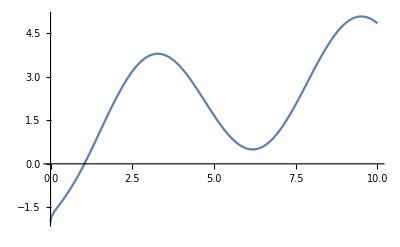

```mathematica
Plot[f[x],{x,0,10}]
```

```mathematica
Задание 2 - поиск вручную с помощью метода хорд;
```

```mathematica
f1[x_]:=Dt[f[x],x];
f2 [x_]:=Dt[f1[x],x];
x[0]=0.5;c=1.5;n=0;
eps=0.001;
m=N[f1[x] /. x->x[0]];
ep=1/m*Abs[f1[x]/.x->x[0]];
Print["n=",n,"  x=",x[n],"  f[x]=",N[f[x]/.x->x[n]],"  Δx=",ep]
While[n<3,x[n+1]=x[n]-N[f[x[n]]*(x[n]-c)/(f[x[n]]-f[c])];ep=1/m*Abs[f[x]/.x->x[n+1]];n++;Print["n=",n,"  x=",x[n],"  f[x]=",N[f[x]/.x->x[n]],"  Δx=",ep]]
```

n=0  x=0.5  f[x]=-1.04806  Δx=1.

n=1  x=0.991739  f[x]=-0.0986086  Δx=0.0591903

n=2  x=1.03415  f[x]=-0.00559161  Δx=0.0033564

n=3  x=1.03654  f[x]=-0.000301138  Δx=0.00018076

```mathematica
Задание 3;
метод секущих;
xa[0]=0.5;xa[1]=1.5;n=0;eps=0.001;ep=1;
Print["n=",n,"  x=",x[n],"  f[x]=",N[f[x]/.x->xa[n]],"  Δx=",ep]
n++;
Print["n=",n,"  x=",x[n],"  f[x]=",N[f[x]/.x->xa[n]],"  Δx=",ep]
While[ep>eps,xa[n+1]=xa[n]-N[f[xa[n]]*(xa[n]-xa[n-1])/(f[xa[n]]-f[xa[n-1]])];ep=Abs[xa[n+1]-xa[n]];n++;Print["n=",n,"  x=",xa[n],"  f[x]=",N[f[xa[n]]],"  Δx=",ep]]
```

n=0  x=0.5  f[x]=-1.04806  Δx=1

n=1  x=0.991739  f[x]=1.08327  Δx=1

n=2  x=0.991739  f[x]=-0.0986086  Δx=0.508261

n=3  x=1.03415  f[x]=-0.00559161  Δx=0.0424061

n=4  x=1.03669  f[x]=0.0000459996  Δx=0.0025492

n=5  x=1.03667  f[x]=-2.05753×10^-8  Δx=0.0000207999

```mathematica
Комбинированный метод;
f2[x]*f[x]/.x->1.5
```

0.0058406

```mathematica
z0=0.5;z1=1.5;xx=1.5;n=0;eps=0.001;ep=1;
Print["n=",n,"  x=",xx,"  z1=",z1,"  Δx=",ep];
While[ep>eps,z1=N[z1-f[z1]*(z0-z1)/(f[z0]-f[z1])];xx=N[x-f[x]/f1[x]/.x->xx];ep=Abs[z1-xx];z0=xx;n++;Print["n=",n,"  x=",xx,"  z1=",z1,"  Δx=",ep];

]
```

n=0  x=1.5  z1=1.5  Δx=1

n=1  x=1.04925  z1=0.991739  Δx=0.0575061

n=2  x=1.0367  z1=1.03657  Δx=0.000129581